```mathematica
(*а)
*)
f[x_]=(Log[3,(5*x^2+1)])^(5*x+3);a=-1;b=3;h=0.2;
```

```mathematica
(*Вычислим количество значений производной на отрезке[-1,3] с шагом h=0,2.*)
n=(b-a)/h;
```

```mathematica
(*Формула второго порядка точности:*)
pro1 [x_] = (f[x+h]-f[x-h])/(2h);
```

```mathematica
(*Составим таблицу:*)
Table[{a+h*i,pro1[a+h*i]},{i,0,n}]
```

{{-1.,1.55801},{-0.8,1.56013},{-0.6,-0.57628},{-0.4,-2.43115},{-0.2,-1.33757},{0.,-0.0669573},{0.2,0.109601},{0.4,1.69218},{0.6,16.1149},{0.8,123.453},{1.,850.739},{1.2,5556.01},{1.4,35313.2},{1.6,221634.},{1.8,1.3852×10^6},{2.,8.66489×10^6},{2.2,5.44162×10^7},{2.4,3.43749×10^8},{2.6,2.18683×10^9},{2.8,1.40203×10^10},{3.,9.06221×10^10}}

```mathematica
(*б)
Нарисуем график производной,точки,которые мы высчитали с помощью функции D пакета Mathematica,точки,соответствующие приближенным значениям производной.
*)
dif[x_]=D[f[x],x];
graphic1 = Plot[dif[x],{x,a,b},PlotRange->{{-1,3}, {-100, 100}}];
graphic2 = ListPlot[Table[{a+h*i,dif[a+h*i]},{i,0,n}], PlotStyle->Red];
graphic3 = ListPlot[Table[{a+h*i,pro1[a+h*i]},{i,0,n}], PlotStyle->Green];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

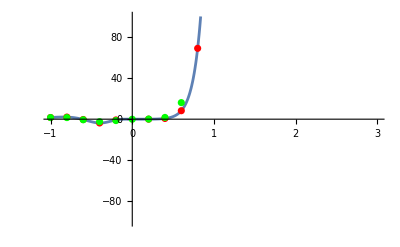

```mathematica
Show[graphic1, graphic2, graphic3]
```